```mathematica
(*continuous functions*)
waux[t_]:=aux[t]
```

```mathematica
wabp[t_]:=(1-aux[t])
```

```mathematica
wrop6[t_]:=aux[t](1-abp[t])
```

```mathematica
wric[t_]:=rop6[t](x[t])
```

```mathematica
wx[t_]:=x[t]
```

```mathematica
wmemt[t_]:=aux[t](1-exo[t])
```

```mathematica
wexo[t_]:=memt[t]
```

```mathematica
wendo[t_]:=(1-memt[t])(1-rop6[t])
```

```mathematica
wpid[t_]:=aux[t](1-pp2a[t])
```

```mathematica
wpp2a[t_]:=pp2a[t](1-pid[t])
```

```mathematica
wabund[t_]:=exo[t]aux[t]
```

```mathematica
wapol[t_]:=abund[t](1-endo[t])pid[t]
```

```mathematica
wbpol[t_]:=abund[t](1-endo[t])pp2a[t]
(*values of the parameter gamma*)
```

```mathematica
b=40;daux=1.;dabp=1.;drop6=7.;dric=1.;dx=1.;dmemt=.5;dexo=1.;dendo=1.;dpid=1.;dpp2a=1.;dabund=1.;dapol=1.;dbpol=1.
```

1.

```mathematica
(*initial values for each node of the network*)
```

```mathematica
aux0=1;abp0=0;rop60=0;ric0=0;x0=1;memt0=1;exo0=1;endo0=0;pid0=1;pp2a0=0;abund0=0;apol0=0;bpol0=0
```

0

```mathematica
(*system of differential equations*)
```

```mathematica
pindy=NDSolve[{aux'[t]==1/(1+Exp[-b(waux[t]-.5)])-daux aux[t],
abp'[t]==1/(1+Exp[-b(wabp[t]-.5)])-dabp abp[t],
rop6'[t]==1/(1+Exp[-b(wrop6[t]-.5)])-drop6 rop6[t],
ric'[t]==1/(1+Exp[-b(wric[t]-.5)])-dric ric[t],
x'[t]==1/(1+Exp[-b(wx[t]-.5)])-dx x[t],
memt'[t]==1/(1+Exp[-b(wmemt[t]-.5)])-dmemt memt[t],
exo'[t]==1/(1+Exp[-b(wexo[t]-.5)])-dexo exo[t],
endo'[t]==1/(1+Exp[-b(wendo[t]-.5)])-dendo endo[t],
pid'[t]==1/(1+Exp[-b(wpid[t]-.5)])-dpid pid[t],
pp2a'[t]==1/(1+Exp[-b(wpp2a[t]-.5)])-dpp2a pp2a[t],
abund'[t]==1/(1+Exp[-b(wabund[t]-.5)])-dabund abund[t],
apol'[t]==1/(1+Exp[-b(wapol[t]-.5)])-dapol apol[t],
bpol'[t]==1/(1+Exp[-b(wbpol[t]-.5)])-dbpol bpol[t],
aux[0]==aux0,abp[0]==abp0,rop6[0]==rop60,ric[0]==ric0,x[0]==x0,memt[0]==memt0,exo[0]==exo0,endo[0]==endo0,pid[0]==pid0,pp2a[0]==pp2a0,abund[0]==abund0,apol[0]==apol0,bpol[0]==bpol0},
{aux[t],abp[t],rop6[t],ric[t],x[t],memt[t],exo[t],endo[t],pid[t],pp2a[t],abund[t],apol[t],bpol[t]},{t,0,20}]
```

{{aux[t]→InterpolatingFunction[{{0.,20.}},<>][t],abp[t]→InterpolatingFunction[{{0.,20.}},<>][t],rop6[t]→InterpolatingFunction[{{0.,20.}},<>][t],ric[t]→InterpolatingFunction[{{0.,20.}},<>][t],x[t]→InterpolatingFunction[{{0.,20.}},<>][t],memt[t]→InterpolatingFunction[{{0.,20.}},<>][t],exo[t]→InterpolatingFunction[{{0.,20.}},<>][t],endo[t]→InterpolatingFunction[{{0.,20.}},<>][t],pid[t]→InterpolatingFunction[{{0.,20.}},<>][t],pp2a[t]→InterpolatingFunction[{{0.,20.}},<>][t],abund[t]→InterpolatingFunction[{{0.,20.}},<>][t],apol[t]→InterpolatingFunction[{{0.,20.}},<>][t],bpol[t]→InterpolatingFunction[{{0.,20.}},<>][t]}}

```mathematica
(*plotting*)
```

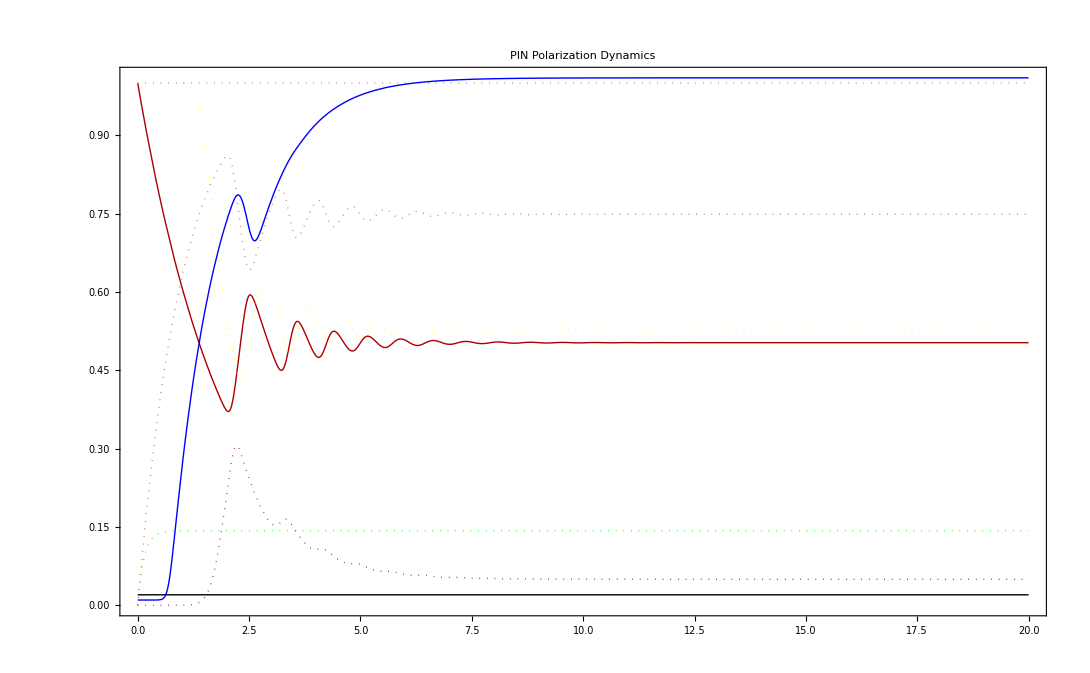

```mathematica
FM1=Plot[Evaluate[{rop6[t],memt[t],exo[t],endo[t],pid[t],0.02+pp2a[t],abund[t],0.01+apol[t]}/.pindy,{t,0,20}],PlotRange->All,Frame->True,PlotStyle->{{Thick,Dotted,Green},{Thick,Darker[Red]},{Thick,Dotted,Yellow},{Thick,Dotted,Purple},{Thick,Dotted, Gray},{Thick,Black},{Thick,Dotted,Brown},{Thick, Blue}},PlotLabel->"PIN Polarization Dynamics"]
```